## @User: ADAPT THIS TO YOUR NEEDS

```mathematica
howManyAtomsInCell=93;
sitestoconsider=Range[1,93];
(*numberofspecies=2; (*Mg Cl*)*)
(*numberofsitesofspecies[#]&/@Range@numberofspecies={62,31};*)
(* remember first timestep has index 1, not 0*)
allsites=Range@howManyAtomsInCell;
sitesCl=Range@62; (* remember that species have not same rlistcutoff *)
sitesMg=Range[63,93];
```

## Extract positions from PIMAIM dumps

```mathematica
Clear[positions];
positions=
Import["/home/levesque/Recherche/Sels-Fondus/MgCl2/mgcl2-inputs/cageCorrelationFunctions/big/positions.out"];
nbTimeSteps=(Length@positions)/howManyAtomsInCell; (* nb of dumps in the file *)
coo[whatAtom_Integer, whatTimestep_Integer] :=coo[whatAtom, whatTimestep]= positions[[howManyAtomsInCell*(whatTimestep-1) + whatAtom]] (* returns the position of atom 1 at timestep t. Note that 1≤i≤N and 0≤t≤9 *)
allPositionsDumpedAtTimestep[whatTimestep_Integer]:=allPositionsDumpedAtTimestep[whatTimestep]=
coo[#,whatTimestep]&/@Range[howManyAtomsInCell] (* set of all (93) positions vectors at time t *)
```

## Lists of neighbours to which apply functions flist

```mathematica
Module[{rlistcutoff=7(* Bohr *)},
list[whatAtom_Integer,whatTimestep_Integer]:=list[whatAtom,whatTimestep]=
HeavisideTheta[rlistcutoff-EuclideanDistance[allPositionsDumpedAtTimestep[whatTimestep][[#]],coo[whatAtom,whatTimestep]]]&/@Range[howManyAtomsInCell];
listCF[sites_List,dt_Integer]:=listCF[sites,dt]=
Mean@Flatten@Outer[list[#,#2].list[#,#2+dt]&,Range@sites,Range@(nbTimeSteps-dt)]/Mean@Flatten@Outer[list[#,#2].list[#,#2]&,Range@sites,Range@nbTimeSteps];
]
```

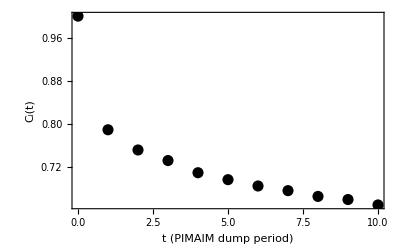

```mathematica
ListPlot[{#,listCF[allsites,#]}&/@Range[0,10],
PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{"t (PIMAIM dump period)","C_l(t)"}]
```

## Number of atoms that have left atom i’s original neighbor list at time t n_i^out(0,t)=|l_i(0)|^2-l_i(0)·l_i(t) Number of atoms that have left between t and t+dt (generalization of previous eq.) n_i^out(t,t+dt)=|l_i(t)|^2-l_i(t)·l_i(t+dt) that we ensemble average over time and sites: n^out=<n_i^out(t,t+dt)> Cage-out correlation function: C_cage^out(t)=⟨Θ(1-n_i^out(t))⟩

```mathematica
Clear[niout,flattenedniout,nout,cageoutCF];
niout[site_Integer,t_Integer,dt_Integer]:=niout[site,t,dt]=list[site,t].list[site,t]-list[site,t].list[site,t+dt]
flattenedniout[dt_Integer]:=flattenedniout[dt]=Flatten@Outer[niout[#,#2,dt]&,sitestoconsider,Range@(nbTimeSteps-dt)]
nout[dt_Integer]:=nout[dt]=Mean@flattenedniout[dt]
cageoutCF[dt_Integer]:=cageoutCF[dt]=Mean@HeavisideTheta[1.001-flattenedniout[dt]]
```

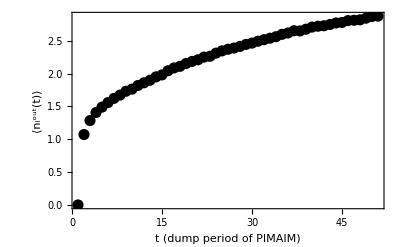

```mathematica
Module[{rangemin=0,rangemax=50},
ListPlot[
Monitor[
nout[#],
Row[{ProgressIndicator[Dynamic[#],{rangemin,rangemax}],#}," /"]
]&/@Range[rangemin,rangemax]
,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{"t (dump period of PIMAIM)","⟨n_i^out(t)⟩"}]
]
```

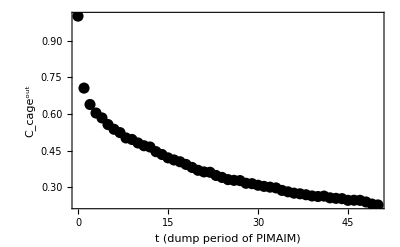

```mathematica
Module[{rangemin=0,rangemax=50},
ListPlot[
Monitor[
{#,cageoutCF[#]},
Row[{ProgressIndicator[Dynamic[#],{rangemin,rangemax}],#}," /"]
]
&/@Range[rangemin,rangemax]
,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{"t (dump period of PIMAIM)","C_cage^out"}
]
]
```